```mathematica
(* Make this notebook standalone *)
(* See: http://stackoverflow.com/questions/4896011/mathematica-separating-notebooks *)
SetOptions[EvaluationNotebook[], CellContext -> Notebook]
```

```mathematica
(* Write down the full WLC model

From "Estimating the Persistence Length of a Worm-Like Chain Molecule ..."
C.Bouchiat,M.D.Wang,et al.Biophysical Journal Volume 76,Issue 1,January 1999,Pages 409-413

web.mit.edu/cortiz/www/3.052/3.052CourseReader/38_BouchiatBiophysicalJ1999.pdf
*)
```

```mathematica
Force = Subscript[k, b]*T/Subscript[L, p] * (1/(4*(1-l)^2) - 1/4 + l + Sum[Subscript[a, i]*l^(i),{i,2,n}])
```

(T k_b (-1/4+1/(4 (1-l)^2)+l+∑_(i=2)^n l^i a_i))/L_p

```mathematica
rules = {l -> x/Subscript[L, 0]-F/Subscript[K, 0]}
```

{l→-F/K_0+x/L_0}

```mathematica
ForceNoCoeffs = Force /. Subscript[a, i]-> 0
```

((-1/4+1/(4 (1-l)^2)+l) T k_b)/L_p

```mathematica
(* Write down the actual numerical coefficients, see ibid... *)
```

```mathematica
coeffs = {
Subscript[a, 0]-> 0,
Subscript[a, 1]->0,
Subscript[a, 2]->-.5164228,
Subscript[a, 3]->-2.737418,
Subscript[a, 4]->16.07497,
Subscript[a, 5]->-38.87607,
Subscript[a, 6]->39.49949,
Subscript[a, 7]->-14.17718};
```

```mathematica
ForceFull = Force /. rules;
```

```mathematica
mRules = {F/Subscript[K, 0]-Subscript[p, 0]/Subscript[L, 0] -> -Subscript[l, 0],-F/Subscript[K, 0]+Subscript[p, 0]/Subscript[L, 0]-> Subscript[l, 0]}
```

{F/K_0-p_0/L_0→-l_0,-F/K_0+p_0/L_0→l_0}

```mathematica
(*
Before we go down a rabbit hole with the extensible model, lets get to know the non-Extensible model...
*)
```

```mathematica
(* Write down the non-extensible model *)
```

```mathematica
NonExtensible = ForceFull /. {F -> 0, n -> 7}
```

(T k_b (-1/4+1/(4 (1-x/L_0)^2)+(x^7 a_7)/L_0^7+(x^6 a_6)/L_0^6+(x^5 a_5)/L_0^5+(x^4 a_4)/L_0^4+(x^3 a_3)/L_0^3+(x^2 a_2)/L_0^2+x/L_0))/L_p

```mathematica
NonExtensibleByRelExtension = NonExtensible /. x -> Subscript[x, rel]*Subscript[L, 0]
```

(T k_b (-1/4+1/(4 (1-x_rel)^2)+x_rel+a_2 x_rel^2+a_3 x_rel^3+a_4 x_rel^4+a_5 x_rel^5+a_6 x_rel^6+a_7 x_rel^7))/L_p

```mathematica
(* Write it in units of Subscript[k, b] T/Subscript[L, p], and x/Subscript[L, 0]*)
```

```mathematica
plotRules = {Subscript[L, p]-> Subscript[k, b]*T}
```

{L_p→T k_b}

```mathematica
RelativeForceNonExt = NonExtensibleByRelExtension  /. plotRules
```

-1/4+1/(4 (1-x_rel)^2)+x_rel+a_2 x_rel^2+a_3 x_rel^3+a_4 x_rel^4+a_5 x_rel^5+a_6 x_rel^6+a_7 x_rel^7

```mathematica
ApproxExpansion = Normal[Series[NonExtensibleByRelExtension,{Subscript[x, rel],0,2}]]
```

(3 T k_b x_rel)/(2 L_p)+(T (3+4 a_2) k_b x_rel^2)/(4 L_p)

```mathematica
RelativeForceNonExtWithCoeffs = RelativeForceNonExt /. coeffs;
```

```mathematica
RelativeForceNonExtNoCoeffs = RelativeForceNonExt /. Subscript[a, i_]-> 0;
```

```mathematica
ApproxPlot = ApproxExpansion /. coeffs /. plotRules
```

(3 x_rel)/2+0.233577 x_rel^2

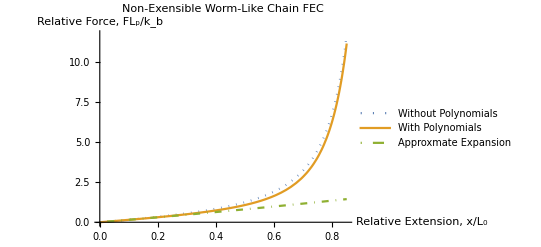

```mathematica
Plot[{RelativeForceNonExtNoCoeffs,RelativeForceNonExtWithCoeffs,ApproxPlot},{Subscript[x, rel],0,0.85},
PlotLabel->"Non-Exensible Worm-Like Chain FEC",
PlotRange->All,
PlotStyle->{Dotted,Thick,{DotDashed,Thick}},
PlotLegends->{"Without Polynomials","With Polynomials","Approxmate Expansion"},
AxesLabel->{"Relative Extension, x/L_0","Relative Force, FL_p/k_b"}]
```

```mathematica
(*
Okay, now for some Jacobian Nastiness
*)
```

```mathematica
(* Start off with some rules to simplify the expressions... *)
```

```mathematica
mRules = {
Subscript[k, b]*T/Subscript[L, p]-> Subscript[c, b,p],
x/Subscript[L, 0]-F/Subscript[K, 0]-> l,
-x/Subscript[L, 0]+F/Subscript[K, 0]-> -l
}
```

{(T k_b)/L_p→c_(b,p),-F/K_0+x/L_0→l,F/K_0-x/L_0→-l}

```mathematica
ConvertToC[expr_] := CForm[expr /. {Subscript[L, 0]-> L0,Subscript[K, 0]-> K0,Subscript[a, i_]-> a[i], Subscript[c, b,p]-> cbp}]
```

```mathematica
DerivWithL0= D[ForceFull,Subscript[L, 0]]  /. mRules /. mRules
```

c_(b,p) (-x/L_0^2-x/(2 (1-l)^3 L_0^2)+∑_(i=2)^n -(i l^(-1+i) x a_i)/L_0^2)

```mathematica
DerivWithK0 = D[ForceFull,Subscript[K, 0]]  /. mRules /. mRules
```

c_(b,p) (F/K_0^2+F/(2 (1-l)^3 K_0^2)+∑_(i=2)^n (F i l^(-1+i) a_i)/K_0^2)

```mathematica
DerivWithForce = D[ForceFull,F] /. mRules /. mRules
```

c_(b,p) (-1/K_0-1/(2 (1-l)^3 K_0)+∑_(i=2)^n -(i l^(-1+i) a_i)/K_0)

```mathematica
DerivWithLp = D[ForceFull,Subscript[L, p]] ;
```

```mathematica
(* Lp has an almost trivial derivative, relative to the actual force... *)
```

```mathematica
DerivWithLpRel = DerivWithLp/ForceFull
```

-1/L_p

```mathematica
ConvertToC[DerivWithL0]
```

cbp*(-(x/Power(L0,2)) - x/(2.*Power(1 - l,3)*Power(L0,2)) + 
     Sum(-((i*Power(l,-1 + i)*x*a(i))/Power(L0,2)),List(i,2,n)))

```mathematica
PlotDeriv = (DerivWithL0 /. {Subscript[c, b,p]-> 1 , n-> 7})/. coeffs /. x -> z*Subscript[L, 0]
```

-z/L_0-z/(2 (1-l)^3 L_0)+(1.03285 l z)/L_0+(8.21225 l^2 z)/L_0-(64.2999 l^3 z)/L_0+(194.38 l^4 z)/L_0-(236.997 l^5 z)/L_0+(99.2403 l^6 z)/L_0

```mathematica
Plot3D[PlotDeriv * Subscript[L, 0],{z,0,1},{l,0,1},
AxesLabel->{"Relvative Extension x/L_0","Relative z=(x/L_0-F/K_0)", "Gradient df/dL_0(units: k_b/L_p)"}]
```

-Graphics3D-